```mathematica
yy=0;
y=.;x=.;z=.;Γ=0.006 2 π;w=0;
zz=-2π w(*+600 Γ Tanh[-6(t-1)]*)(*+D[ 4 Sin[2π *17t-6Sin[2π 0.5(1/1) t]],t]*);
s=0.55 10^5;
R={Sin[θ[t]]Cos[ϕ[t]],Sin[θ[t]]Sin[ϕ[t]],Cos[θ[t]]};
R1={x[t],y[t],z[t]};
SeedRandom[];
(*bb=RandomReal[{0.95,1.05},13];*)
(*Ω11=√(s/2) Γ Sum[bb[[n+1]]Sin[2π 5(t-0.12n)]Boole[t>=0.12n&&t≤(0.12n+0.1)],{n,0,12}];*)
(*aa={0,9,42,11,8,37,2,37,8,11,42,9,0}π/24;*)
(*ϕ11=Sum[aa[[n+1]]Boole[t>=0.12n&&t≤(0.12n+0.1)],{n,0,12}];*)

(*Ω={Ω11 Cos[ϕ11],Ω11 Sin[ϕ11],0};*)
θ1=(5π/6(Boole[t>=1.1&&t≤2.1]+Boole[t≥3.3&&t≤4.3])+π/3Boole[t≥2.2&&t≤3.2]);
ψ=Sum[√(s/2) Γ Sin[2π 0.5 (t-τ)]^2 Boole[(t-τ)>=0&&(t-τ)≤1],{τ,0,4.4,1.1}];
Ω={ψ Cos[θ1],ψ Sin[θ1],zz+3};
t0=3;
a=NDSolve[{D[R1,t]==Cross[Ω,R1],x[0]==0,y[0]==0,z[0]==-1},{x,y,z},{t,0,2 t0},MaxSteps->1000000];
RR=R1/.a;
RRR=RR/.t->2t0;
(RRR[[1,3]]+1)/2;
(*Print[(RRR[[1,3]]-1)/-2];*)
(*yy=yy+(RRR[[1,3]]-1)/-2;*)
Manipulate[r=Flatten[RR/.t->t1];h=zz/.t->t1;
(*r2=1/(√(s/2) Γ){Ω11 Cos[ϕ11]/.t->t1,Ω11 Sin[ϕ11]/.t->t1,0};*)
r2=1/6 Ω/.t->t1;Show[Graphics3D[{Blue,Arrowheads[0.04],Arrow@Tube[{{0,0,0},{r2[[1]],r2[[2]],r2[[3]]}},0.01]}],Graphics3D[{Red,Arrowheads[0.03],Arrow[Tube[{{0,0,0},{r[[1]],r[[2]],r[[3]]}},0.01]]}],Graphics3D[{Opacity[.5],Sphere[{0,0,0}]}],Graphics3D[{Opacity[0],Sphere[{0,0,0},1.5]}],ParametricPlot3D[RR,{t,0,t1},PlotRange->All,PlotPoints->1000]],{t1,0.000001,2t0}]
RR/.t->2t0
(%[[1,3]]+1)/2
(%%[[1,3]]-1)/-2
```

{{0.301004,0.13257,0.944363}}

0.972182

0.0278183

```mathematica
yy/200
```

0.966502

```mathematica
yy/20
```

0

```mathematica
RR/.t->2t0
(%[[1,3]]+1)/2
(%%[[1,3]]-1)/-2
```

{{0.00161119,0.00517039,-0.999985}}

7.33776×10^-6

0.999993

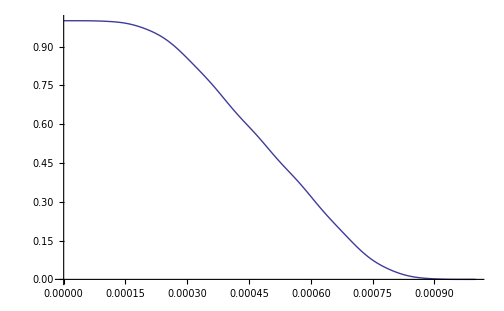

```mathematica
Plot[1-(RR[[1,3]]-1)/-2,{t,0,10^-3},PlotPoints->1000,PlotRange->{0,1}]
```

```mathematica
?Sphere
```

Sphere[{x,y,z},r] 显示一个以 r 为半径， (x,y,z) 为球心的球体.
Sphere[{x,y,z}] 显示一个半径为1的球体.
Sphere[{{x_1,y_1,z_1},{x_2,y_2,z_2},…},r] 显示以半径为 r 的球体集合.

```mathematica
2π 20. 10^3
1800. Γ
```

125664.

67858.4

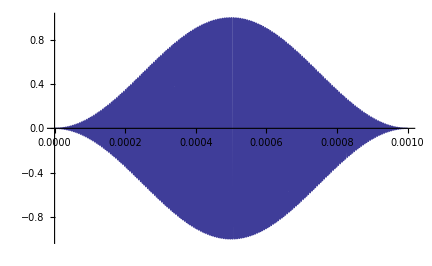

```mathematica
Plot[Sin[2π 0.5 10^3 t]^2 Sin[2π 200 10^3 t],{t,0,10^-3},PlotPoints->2000]
```

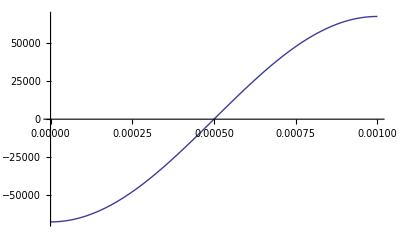

```mathematica
Plot[1800 Γ Sin[2π 10^3(1/2(t1-π/(2π 10^3))+π/(2π 10^3))-π],{t1,0,10^-3}]
```

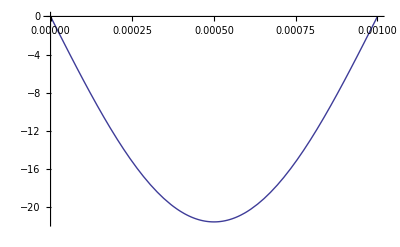

```mathematica
Integrate[1800 Γ Sin[2π 10^3(1/2(t1-π/(2π 10^3))+π/(2π 10^3))-π],{t1,0,t}];
Plot[%,{t,0,10^-3}]
```